```mathematica
T={{Exp[β+h],Exp[-β]},{Exp[-β], Exp[β-h]}}
```

{{ⅇ^(h+β),ⅇ^-β},{ⅇ^-β,ⅇ^(-h+β)}}

```mathematica
eig=Eigenvalues[T]
```

{1/2 ⅇ^(-h-β) (ⅇ^(2 β)+ⅇ^(2 h+2 β)-√(4 ⅇ^(2 h)+ⅇ^(4 β)-2 ⅇ^(2 h+4 β)+ⅇ^(4 h+4 β))),1/2 ⅇ^(-h-β) (ⅇ^(2 β)+ⅇ^(2 h+2 β)+√(4 ⅇ^(2 h)+ⅇ^(4 β)-2 ⅇ^(2 h+4 β)+ⅇ^(4 h+4 β)))}

```mathematica
eig/.h->0
```

{1/2 ⅇ^-β (-2+2 ⅇ^(2 β)),1/2 ⅇ^-β (2+2 ⅇ^(2 β))}

```mathematica
n=.
```

```mathematica
Δ=4Exp[-2 β]+2 Exp[2β](Cosh[ 2h]-1)
```

4 ⅇ^(-2 β)+2 ⅇ^(2 β) (-1+Cosh[2 h])

```mathematica
Z=Total[eig^n]
```

2^-n (ⅇ^(-h-β) (ⅇ^(2 β)+ⅇ^(2 h+2 β)-√(4 ⅇ^(2 h)+ⅇ^(4 β)-2 ⅇ^(2 h+4 β)+ⅇ^(4 h+4 β))))^n+2^-n (ⅇ^(-h-β) (ⅇ^(2 β)+ⅇ^(2 h+2 β)+√(4 ⅇ^(2 h)+ⅇ^(4 β)-2 ⅇ^(2 h+4 β)+ⅇ^(4 h+4 β))))^n

```mathematica
z=(2Exp[β]Cosh[h]-Sqrt[Δ])^n +(2Exp[β]Cosh[h]+Sqrt[Δ])^n
```

(2 ⅇ^β Cosh[h]-√(4 ⅇ^(-2 β)+2 ⅇ^(2 β) (-1+Cosh[2 h])))^n+(2 ⅇ^β Cosh[h]+√(4 ⅇ^(-2 β)+2 ⅇ^(2 β) (-1+Cosh[2 h])))^n

```mathematica
Z/.{β->1.0,h->1.0}
z/(2^n)/.{β->1.0,h->1.0}
```

0.978887^n+7.41017^n

2^-n (1.95777^n+14.8203^n)

```mathematica
M[β_,h_,n_]=D[Log[z],h]
```

(n (2 ⅇ^β Cosh[h]-√(4 ⅇ^(-2 β)+2 ⅇ^(2 β) (-1+Cosh[2 h])))^(-1+n) (2 ⅇ^β Sinh[h]-(2 ⅇ^(2 β) Sinh[2 h])/(√(4 ⅇ^(-2 β)+2 ⅇ^(2 β) (-1+Cosh[2 h]))))+n (2 ⅇ^β Cosh[h]+√(4 ⅇ^(-2 β)+2 ⅇ^(2 β) (-1+Cosh[2 h])))^(-1+n) (2 ⅇ^β Sinh[h]+(2 ⅇ^(2 β) Sinh[2 h])/(√(4 ⅇ^(-2 β)+2 ⅇ^(2 β) (-1+Cosh[2 h])))))/((2 ⅇ^β Cosh[h]-√(4 ⅇ^(-2 β)+2 ⅇ^(2 β) (-1+Cosh[2 h])))^n+(2 ⅇ^β Cosh[h]+√(4 ⅇ^(-2 β)+2 ⅇ^(2 β) (-1+Cosh[2 h])))^n)

```mathematica
M[0,1.,32]
```

24.371

```mathematica
χ[β_,n_]:= D[M[β,h,n],h]/n/.h->0
```

```mathematica
χ[1.0,32]
```

7.38663

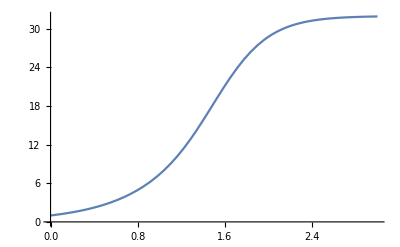

```mathematica
Plot[χ[β,32],{β,0,3}]
```

```mathematica
χ[0.0]
```

32.